# Leads connected to 1 - 10 and 1 to 10

# a1 and a2

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
leads[25]
```

{{{0.-0.848854 ⅈ,0.500319+0. ⅈ,0.+0.170564 ⅈ,-0.00148296+0. ⅈ,0.+0.0219777 ⅈ,0.00302035+0. ⅈ,0.+0.0116615 ⅈ,-0.00381066+0. ⅈ,0.+0.0000550464 ⅈ,0.0030296+0. ⅈ,0.+0.00421847 ⅈ,3,0.+0.000839972 ⅈ,-0.0000187093+0. ⅈ,0.+0.000473503 ⅈ,3.77068×10^-6+0. ⅈ,0.+0.000321694 ⅈ,-0.0000155762+0. ⅈ,0.+0.000184309 ⅈ,4.2504×10^-6+0. ⅈ,0.+0.000109971 ⅈ,-1.79988×10^-6+0. ⅈ,0.+0.0000334653 ⅈ},23,{1}},299,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25]],concentration],RandomSample[Join[s[1,50,26,50]],total-concentration]],First],10000]
```

```mathematica
dist[50,10]
```

{1}
 |  |  |  |

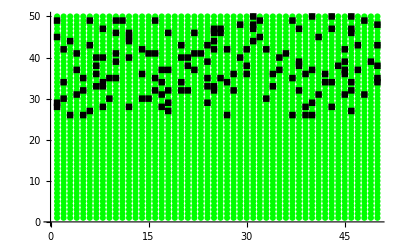

```mathematica
ListPlot[{Join[s[1,50,1,50]],dist[150,0][[1]]},PlotMarkers->Automatic,PlotStyle->{Green,Black}]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,10}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=10,abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[0,0.0001,1,0,1,150,70,1]
```

2.42541

```mathematica
Table[{m,Print[m];Mean[ParallelTable[CA[1.5,0.0001,1,0,1,150,m,n],{n,1000}]]},{m,10,150,20}]
```

10

30

50

70

90

110

130

150

{{10,2.3043},{30,2.19258},{50,2.02244},{70,1.84046},{90,1.71503},{110,1.55248},{130,1.41465},{150,1.29012}}

```mathematica
Show[]
```

```mathematica
Table[Export["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,150,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,10,140,10}]
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

{/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_10_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_20_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_30_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_40_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_50_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_60_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_70_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_80_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_90_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_100_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_110_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_120_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_130_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_140_.dat}

```mathematica
transmission=Table[{x,Import["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_1_10/up_down/1_2/ϵ1_150_"<>ToString[x]<>"_.dat"]},{x,10,140,10}]
```

{{10,{{0.,1.79013},{0.01,1.69997},{0.02,1.65448},{0.03,1.76579},{0.04,1.73287},{0.05,2.06761},{0.06,2.48983},{0.07,3.3705},{0.08,7.32068},{0.09,3.38868},{0.1,1.75858},{0.11,1.44485},277,{2.89,0.953248},{2.9,0.897285},{2.91,0.88761},{2.92,0.942064},{2.93,0.95639},{2.94,1.07406},{2.95,1.08553},{2.96,1.11126},{2.97,1.14532},{2.98,1.18945},{2.99,1.19749},{3.,1.13264}}},12,{140,{1}}}
 |  |  |  |

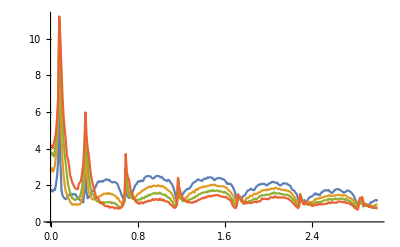

```mathematica
ListLinePlot[Table[transmission[[x]],{x,1,14,4}],PlotRange->All]
```

```mathematica
Clear[input]
```

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
input= Monitor[Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,150,70,n]},{ω,Range[0,3,0.01]}],{n,800,900}],n]
```

{{{0.,4.59561},{0.01,3.15041},{0.02,1.90248},{0.03,2.49999},{0.04,3.49798},{0.05,4.055},{0.06,3.47361},{0.07,8.13015},{0.08,10.4511},{0.09,7.02676},{0.1,1.14539},{0.11,0.183927},277,{2.89,0.804857},{2.9,1.25997},{2.91,0.557836},{2.92,1.10574},{2.93,1.12303},{2.94,0.652117},{2.95,0.608427},{2.96,0.669108},{2.97,0.0270291},{2.98,0.0502742},{2.99,0.396489},{3.,0.714157}},99,{1}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{14,2}

```mathematica
Clear[misfit]
```

```mathematica
misfit[x_,y_,n_]:=misfit[x,y,n]=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,14}];lista=ρ1;
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

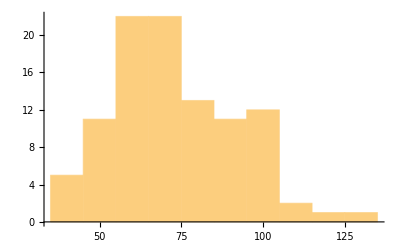

```mathematica
Table[misfit[2.5,0.4,n][[2]][[1]],{n,100}]//Histogram
```

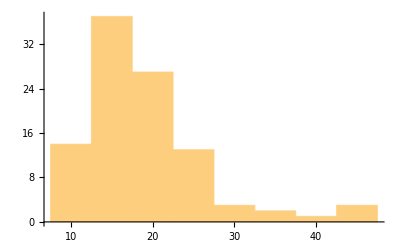

```mathematica
Histogram[%34]
```

```mathematica
misfit1[x_,y_,z_]:= 1/(x-y+0.01)
```

```mathematica
Table[{0.5,y},{y,0.14,0.5,0.02}]
```

{{0.5,0.14},{0.5,0.16},{0.5,0.18},{0.5,0.2},{0.5,0.22},{0.5,0.24},{0.5,0.26},{0.5,0.28},{0.5,0.3},{0.5,0.32},{0.5,0.34},{0.5,0.36},{0.5,0.38},{0.5,0.4},{0.5,0.42},{0.5,0.44},{0.5,0.46},{0.5,0.48},{0.5,0.5}}

```mathematica
d1[x_,n_]:=d1[x,n]=Mean[Table[misfit[x,y,n][[1]],{y,0.4,x-0.1,0.02}]]
```

```mathematica
Clear[d1]
```

```mathematica
xxx=Monitor[Table[Mean[ParallelTable[d1[x,n],{x,Range[0.75,2.7,0.05]}]],{n,100}],n]
```

```mathematica
Table[xxx[[x]][[Position[xxx[[x]],Min[xxx[[x]]]][[1,1]]]][[1]],{x,100}]
```

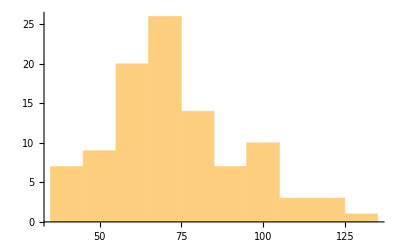

```mathematica
Histogram[%78]
```

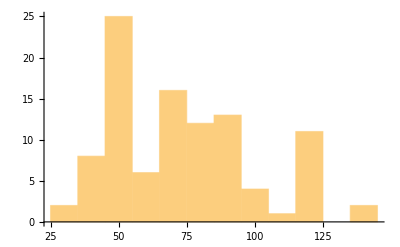

```mathematica
Histogram[%60]
```

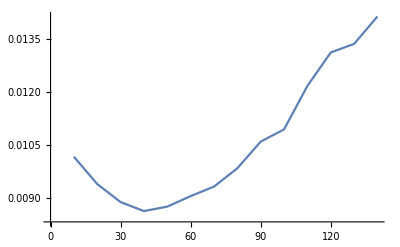
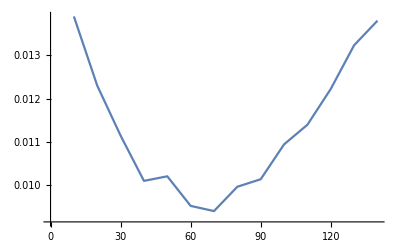
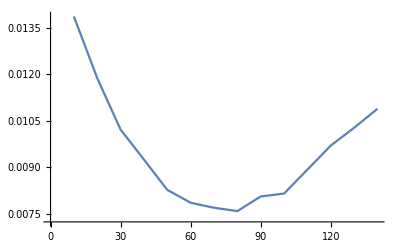
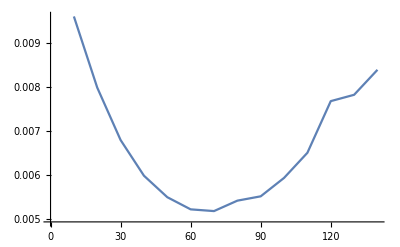
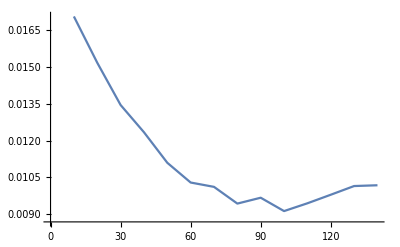
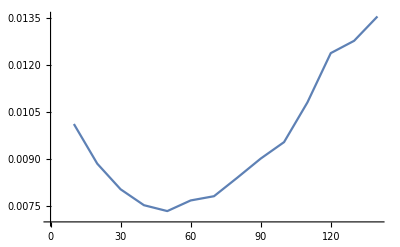
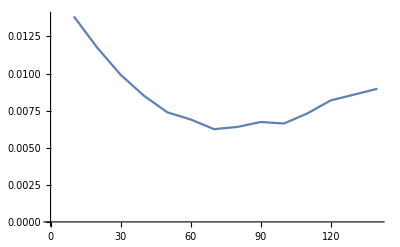
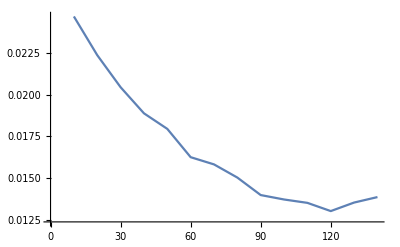

```mathematica
Table[ListLinePlot[%50[[x]]],{x,10}]
```

```mathematica
Table[misfit[3,0.15,n][[2]][[1]],{n,100}]
```

{40,70,70,70,100,50,70,120,40,50,70,100,90,80,110,50,120,40,80,70,90,120,60,90,50,80,50,80,70,70,70,70,120,50,80,50,70,70,120,60,70,80,50,60,70,120,90,90,60,70,100,90,90,50,90,50,90,90,90,60,80,50,50,50,80,130,50,50,50,50,60,50,70,80,50,120,80,50,50,60,120,120,80,50,70,50,50,120,50,90,120,70,90,80,50,70,140,50,50,50}

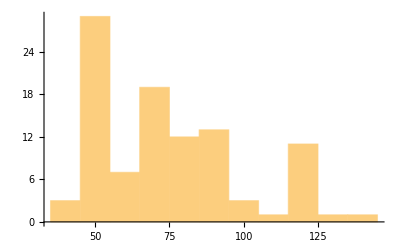

```mathematica
Histogram[%47]
```

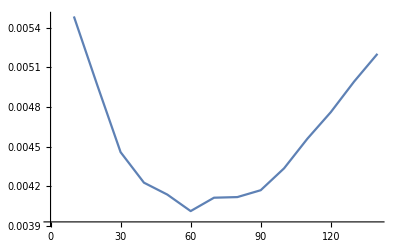

```mathematica
ListPlot[%42,Joined->True]
```

```mathematica
Mean[ParallelTable[d1[x,2],{x,Range[0.5,2.7,0.05]}]]
```

{{10,0.010287},{20,0.00903561},{30,0.00822819},{40,0.00755574},{50,0.00771744},{60,0.00747598},{70,0.00752387},{80,0.00816145},{90,0.00834585},{100,0.00911876},{110,0.00964584},{120,0.0104238},{130,0.0111277},{140,0.0117237}}

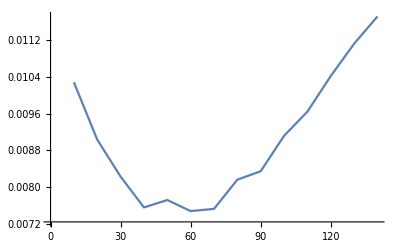

```mathematica
ListPlot[%40,Joined->True]
```

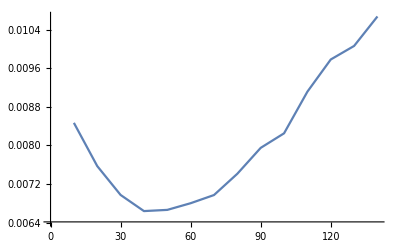

```mathematica
ListPlot[%38,Joined->True]
```

```mathematica
Mean[ParallelTable[d1[x,2],{x,Range[0.5,2.7,0.05]}]]
```

{{5,0.00649115},{10,0.00592942},{15,0.00548025},{20,0.00540098},{25,0.00504826},{30,0.00504162},{35,0.00496757},{40,0.00497253},{45,0.00512267}}

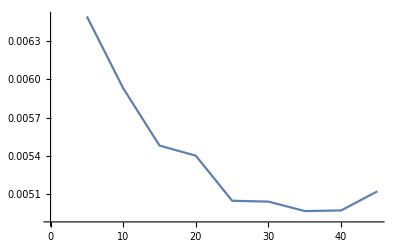

```mathematica
ListPlot[%96,Joined->True]
```

```mathematica
N[x]
```

{38.1346,29.0701,18.1124,38.0967,24.4058,31.632,34.031,19.7254,33.864,39.1732,16.2131,24.8279,26.0485,29.3249,21.0025,23.9422,32.4113,40.6876,26.6228,20.9885,29.985,30.2052,28.784,19.2043,34.1078,25.6453,28.4612,25.9863,37.7376,34.0719,13.1701,37.9928,28.3105,15.3431,38.9652,20.3836,28.5564,25.7685,26.2307,25.2964,10.438,22.1693,21.0025,38.0711,31.8215,32.4591,23.2944,30.838,13.8923,33.0629,20.3336,18.5121,18.1365,29.8964,21.0496,21.1753,31.6123,22.7714,42.0015,27.0754,19.5901,29.0067,32.8904,40.9915,31.4409,33.739,29.5815,31.3735,33.3304,23.1525,26.3553,14.2802,29.3058,23.3204,21.9211,30.5501,24.2001,25.6068,36.2701,41.0013,36.7365,37.8374,17.9167,37.4961,32.0211,27.3989,32.7762,26.3848,25.5715,26.5028,22.207,35.295,13.6991,18.0928,40.432,29.3604,35.9818,37.0859,33.4078,27.7696}

```mathematica
Module[{i=0},Do[If[40>x[[y]]>20,i++,i],{y,100}];i]
```

80

```mathematica
N[StandardDeviation[x]]
```

7.36889

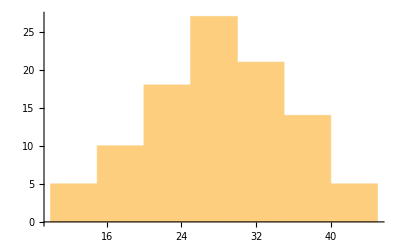

```mathematica
Histogram[x]
```

```mathematica
Mean[Abs[Transpose[%46][[1]]-20]/20]//N
```

0.24126

```mathematica
Mean[Table[Print[nnn];Mean[Table[Mean[Table[misfit[xx,yy,nnn],{yy,Range[0.15+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]]
```

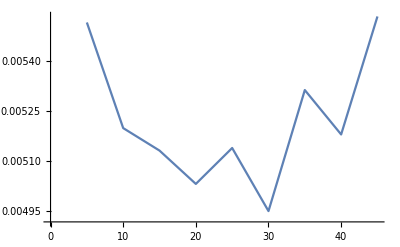

```mathematica
ListLinePlot[%27]
```

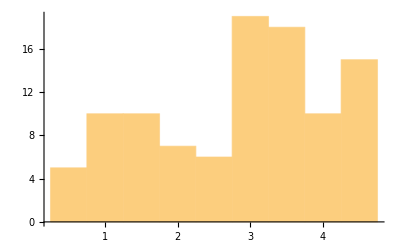

```mathematica
Histogram[%172]
```

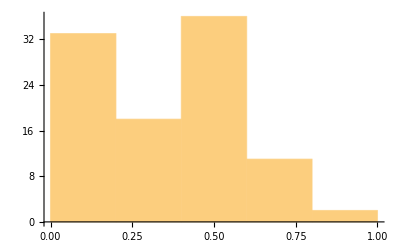

```mathematica
Histogram[%151]
```